# Supplementary tensors

The direct calculation time of tensors is irrelevant since the code uses memoization. When the code calculates a tensor, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

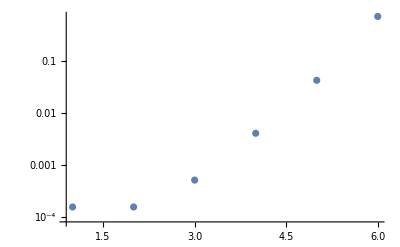

```mathematica
ListLogPlot[Table[Timing[ITensor[DummyArray[n]]][[1]],{n,6}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.0000356925 seconds

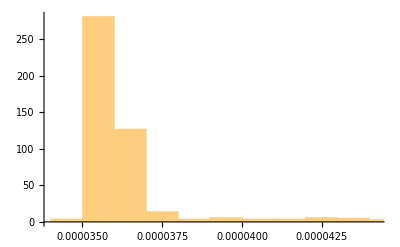

```mathematica
Table[Timing[ITensor[DummyArray[6]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

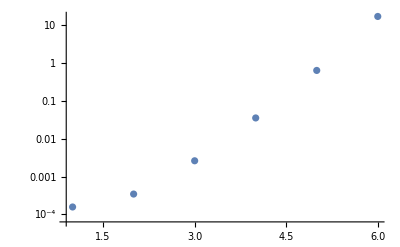

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{},DummyArray[n]]][[1]],{n,6}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.000216248 seconds

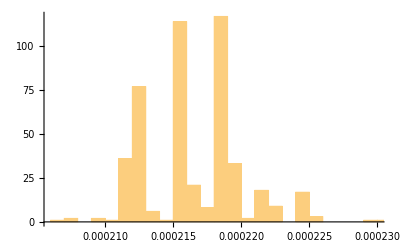

```mathematica
Table[Timing[CTensorGeneral[{},DummyArray[6]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

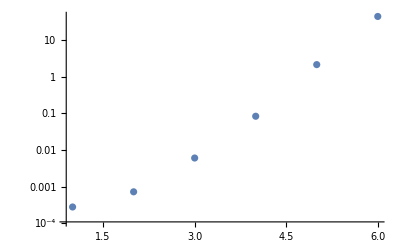

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1},DummyArray[n]]][[1]],{n,6}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.000035 seconds

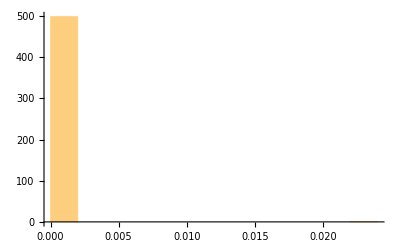

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1},DummyArray[6]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

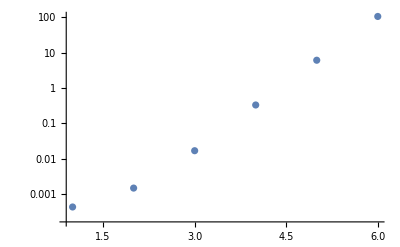

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[n]]][[1]],{n,6}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.00003505 seconds

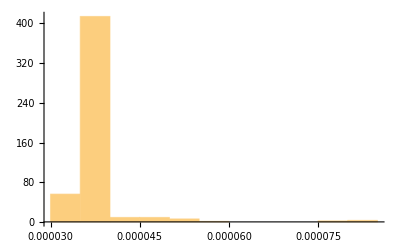

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[6]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C3Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

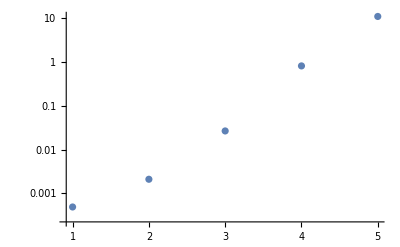

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[n]]][[1]],{n,5}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.0000300875 seconds

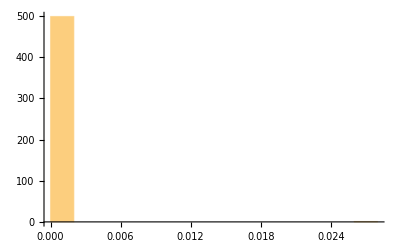

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[5]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C4Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

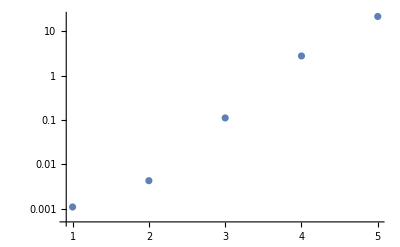

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[n]]][[1]],{n,5}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.0000296875 seconds

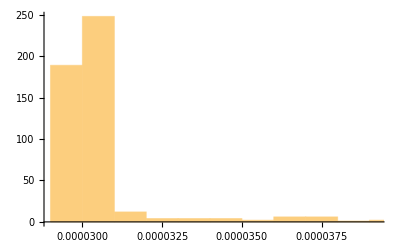

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[5]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C5Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

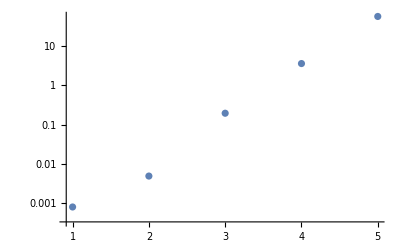

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},DummyArray[n]]][[1]],{n,5}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.000030045 seconds

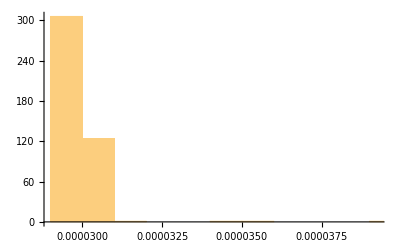

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},DummyArray[5]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

## C6Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

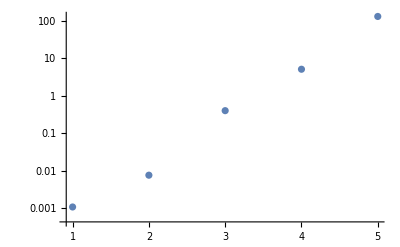

```mathematica
ListLogPlot[Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5,μ6,ν6},DummyArray[n]]][[1]],{n,5}],PlotRange->All]
```

-Graphics-

The trimmed mean evaluation time is 0.000030245 seconds

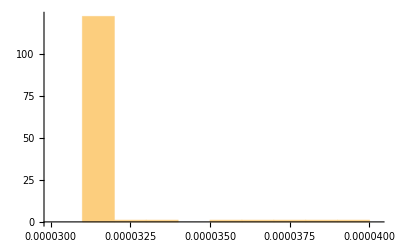

```mathematica
Table[Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5,μ6,ν6},DummyArray[5]]][[1]],{n,500}];
Show[ListPlot[%,PlotMarkers->"x",AxesOrigin->{0,0},PlotRange->{{0,501},{0,1.2Max[%]}},PlotStyle->Black],Plot[{TrimmedMean[%,0.1],TrimmedMean[%,0.1]-StandardDeviation[%],TrimmedMean[%,0.1]+StandardDeviation[%]},{x,0,500},PlotStyle->{Black,Blue,Red},PlotLegends->{"TrimmedMean","TrimmedMean-StandardDeviation","TrimmedMean+StandardDeviation"}],ImageSize->Large]
Print["The trimmed mean evaluation time is "<>ToString[DecimalForm[TrimmedMean[%%,0.1]]]<>" seconds"]
Histogram[%%%]
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Kinetic term

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.016103,0.023991,0.199049,2.77347,44.8188}

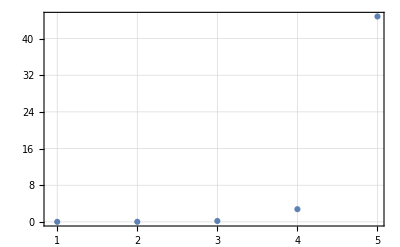

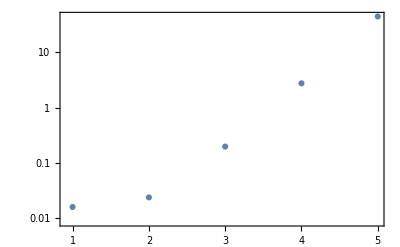

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
Table[Timing[GravitonScalarVertex[DummyArray[n],p1,p2,m]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Potential term

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.000471,0.000626,0.003192,0.038478,0.714088}

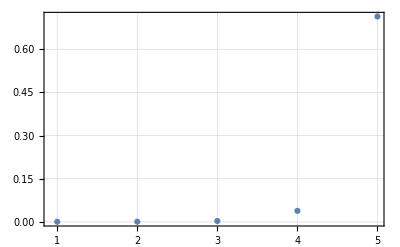

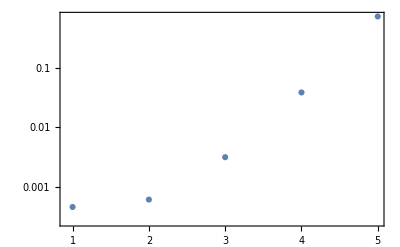

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
Table[Timing[GravitonScalarPotentialVertex[DummyArray[n],λ]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton-fermion vertex

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.005099,0.021947,0.364244,3.58896,150.084}

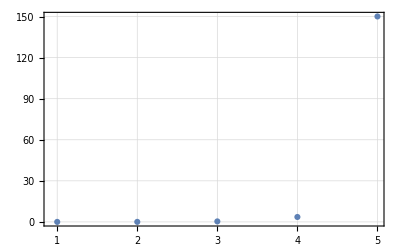

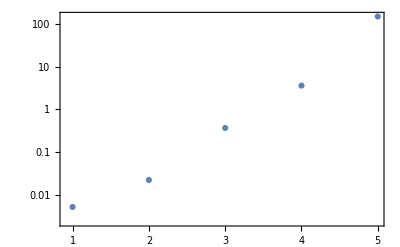

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
Table[Timing[GravitonFermionVertex[DummyArray[n],p1,p2,m]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton-vector vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Massive vectors

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.035743,0.232109,3.09437,54.7461,893.594}

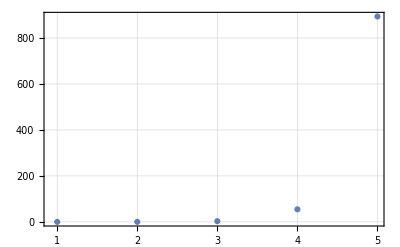

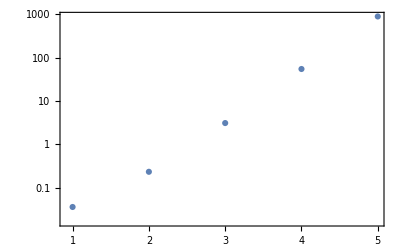

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonMassiveVectorVertex[DummyArray[n],λ1,p1,λ2,p2,m]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Massless vectors

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.058493,0.674379,12.5426,372.343}

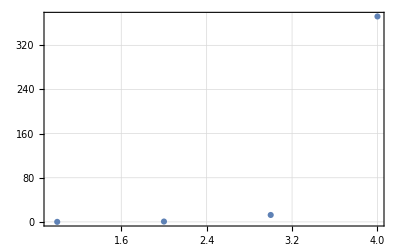

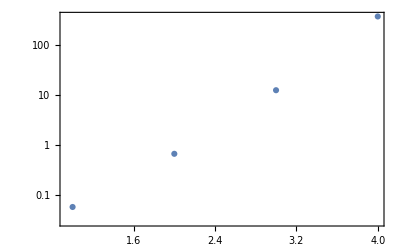

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonVectorVertex[DummyArrayK[n],λ1,p1,λ2,p2,ε]][[1]],{n,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Ghosts

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.004132,0.017367,0.18074,2.4578,43.0992}

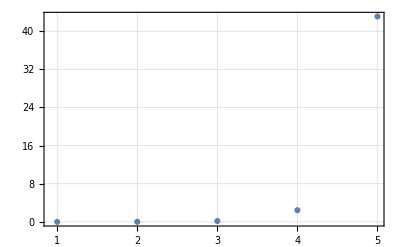

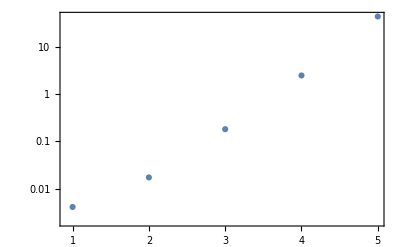

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
Table[Timing[GravitonVectorGhostVertex[DummyArray[n],p1,p2]][[1]],{n,5}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

# Graviton vertices

The direct calculation time is irrelevant since the code uses memoization. When the code calculates a quantity, it records the result in memory. When it requires the expression again, it takes the value from memory and does not calculate it again.

## Pure graviton vertices

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{6.58279,297.311}

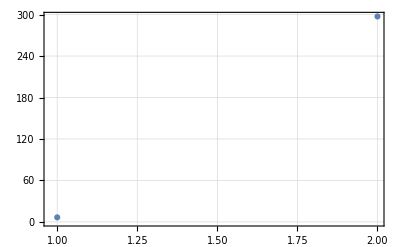

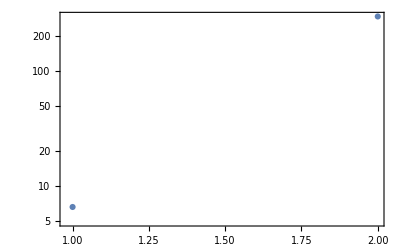

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
Table[Timing[GravitonVertex[DummyArrayK[n],ε]][[1]],{n,3,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```

## Graviton-ghost vertex

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.050258,0.958687,18.7448,505.261}

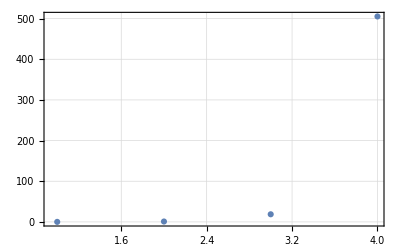

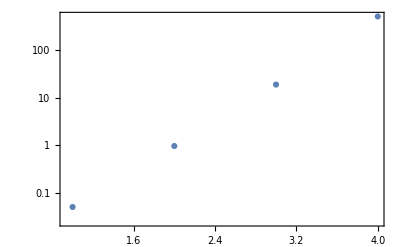

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
Table[Timing[GravitonGhostVertex[DummyArrayK[n],λ1,p1,λ2,p2]][[1]],{n,1,4}]
ListPlot[%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
ListLogPlot[%%,PlotRange->All,PlotMarkers->Automatic,PlotTheme->"Detailed"]
NotebookSave[]
```